# Population Control Analysis

HMSC

Description: Imports all the CSV files in a directory containing individual interventions for effectiveness comparison. Created for analysis of the routines found in: “Outputs/IndependentCMEffects”
-CSV files must have headers indicating the column tag for easy filtering
-Naming convention is: covZZZY.Y___.csv where Y.Y is the coverage level
-Requires manual tags to be setup

## Functions

```mathematica
PlotReview[scores_,name_]:=Module[{bas,are,eav,irs,itn,ivm,ovi,zoo},
bas=scores[[1]];are=scores[[2]];eav=scores[[3]];irs=scores[[4]];
itn=scores[[5]];ivm=scores[[6]];ovi=scores[[7]];zoo=scores[[8]];
ListPolarPlot[
{
{
{0,bas},{45Degree,are},{90Degree,eav},{135Degree,irs},{180Degree,zoo},
{225Degree,itn},{270Degree,ivm},{315Degree,ovi},{360Degree,bas}
}
},
PlotMarkers->{Automatic,Large},
Joined->True,
ImageSize->500,
PlotStyle->{{LightRed,Thickness[.01]}},
PlotRange->{{-225,225},{-225,225}},
Epilog->{
Style[Text["Coverage: "<>ToString[name]<>"%",{0,200}],Bold,Purple,30],
Style[Text["BAS",{120,0}],Bold,12,White],
Style[Text["ARE",{90,90}],Bold,12,White],
Style[Text["ZOO",{-120,0}],Bold,12,White],
Style[Text["EAV",{0,120}],Bold,12,White],
Style[Text["ITN",{-90,-90}],Bold,12,White],
Style[Text["IVM",{0,-120}],Bold,12,White],
Style[Text["IRS",{-90,90}],Bold,12,White],
Style[Text["OVI",{90,-90}],Bold,12,White]
},
InterpolationOrder->1,
AxesStyle->Directive[LightGray,8],
Axes->True,
GridLinesStyle->Directive[Thickness[.005],Dashed,LightBlue],
PolarGridLines->{Table[i*Degree,{i,0,360,45}],Range[0,250,25]}
]
]
PlotReview2[scores_,name_,color_]:=Module[{bas,are,eav,irs,itn,ivm,ovi,zoo},
bas=scores[[1]];are=scores[[2]];eav=scores[[3]];irs=scores[[4]];
itn=scores[[5]];ivm=scores[[6]];ovi=scores[[7]];zoo=scores[[8]];
ListPolarPlot[
{
{
{0,bas},{45Degree,are},{90Degree,eav},{135Degree,irs},{180Degree,zoo},
{225Degree,itn},{270Degree,ivm},{315Degree,ovi},{360Degree,bas}
}
},
PlotMarkers->{Automatic,Tiny},
Joined->True,
ImageSize->500,
PlotStyle->{{color,Thickness[.003]}},
PlotRange->{{-250,250},{-250,250}},
Epilog->{
Style[Text["BAS",{210,0}],20],
Style[Text["ARE",{140,140}],20],
Style[Text["ZOO",{-210,0}],20],
Style[Text["EAV",{0,210}],20],
Style[Text["ITN",{-140,-140}],20],
Style[Text["IVM",{0,-210}],20],
Style[Text["IRS",{-140,140}],20],
Style[Text["OVI",{140,-140}],20]
},
InterpolationOrder->1,
AxesStyle->Directive[Gray,10],
Axes->True,
GridLinesStyle->Directive[Thickness[.0005],Dashed,Gray],
PolarGridLines->{Table[i*Degree,{i,0,360,45}],Range[0,250,50]}
]
]
Magnitude[x_,y_]:=Sqrt[x^2+y^2]
PolarToRectangular[degree_,magnitude_]:={magnitude*Cos[degree Degree],magnitude*Sin[degree Degree]}
CreateLayer[values_,z_]:=Module[{pairs,polars},
pairs=({Range[0,359,(360/Length[values])]//N,values//N}//Transpose);
polars=PolarToRectangular[#[[1]],#[[2]]]&/@pairs;
{#[[1]],#[[2]],z}&/@polars
]
PolarToRectangular2[degree_,magnitude_]:={magnitude*Cos[degree +.215],magnitude*Sin[degree+.215]}
PolarToRectangular3[degree_,magnitude_]:={magnitude*Cos[degree+.215],magnitude*Sin[degree+.215]}
```

```mathematica
PolarToRectangularCoordinates[degree_,magnitude_]:={magnitude*Cos[degree ],magnitude*Sin[degree]}
Options[RadialPlot]={Frame->False,FontSize->15,FontAngle->45Degree,PlotMarkers->{Automatic,Medium},Joined->True,PlotStyle->{{Thickness[.005]}},AxesStyle->Directive[Gray,10],Axes->True,GridLinesStyle->Directive[Thickness[.001],LightBlue],PlotRange->Automatic,PolarGridLines->Automatic};
RadialPlot[values_,labels_,OptionsPattern[]]:=Module[{degreeIncrement,list,graph,degrees,transposed,max,labelsPairs,sample=values},
degreeIncrement=(360/(sample//Length))Degree;
degrees=Range[0,(360-1)Degree,degreeIncrement];
transposed=Transpose[{degrees,sample}];
labelsPairs=Transpose[{labels,PolarToRectangularCoordinates[#,(max+max*.25)]&/@degrees}];
max=Max[transposed[[All,2]]];
list=ListPolarPlot[
Append[transposed,First[transposed]]
,Frame->OptionValue[Frame]
,Epilog->{Rotate[Style[Text[#[[1]],#[[2]]],Bold,OptionValue[FontSize]],OptionValue[FontAngle]]&/@labelsPairs}
,PlotMarkers->OptionValue[PlotMarkers]
,Joined->OptionValue[Joined]
,PlotStyle->OptionValue[PlotStyle]
,InterpolationOrder->1
,AxesStyle->OptionValue[AxesStyle]
,Axes->OptionValue[Axes]
(*,GridLines->ConstantArray[Range[-max*2,max*2,100],2]*)
(*,GridLinesStyle->OptionValue[GridLinesStyle]*)
,PlotRange->If[OptionValue[PlotRange]==Automatic,{{-(max+max*.5),max+max*.5},{-(max+max*.5),max+max*.5}},OptionValue[PlotRange]]
(*,PolarGridLines->If[OptionValue[PolarGridLines]==Automatic,{Table[i,{i,0,360,degreeIncrement}],Range[0,10000,50]},OptionValue[PolarGridLines]]*)];
graph=Graphics[{
Gray,
Thin,
Circle[{0,0},#]&/@Range[0,max,25],
Line[{{0,0},#}]&/@(PolarToRectangularCoordinates[#,Max[Range[0,max,50]]]&/@degrees)
}];
Show[{list,graph}]
]
Options[RadialPlotRange]={Frame->False,FontSize->15,ImageSize->Medium,FontAngle->45Degree,PlotMarkers->{Automatic,Tiny},Joined->True,PlotStyle->{{Thickness[.005]}},AxesStyle->Directive[Gray,10],Axes->True,GridLinesStyle->Directive[Thickness[.0025],Dashed,Gray],PlotRange->Automatic,PolarGridLines->Automatic};
RadialPlotRange[values_,labels_,range_,labelDistance_,gridLines_,OptionsPattern[]]:=Module[{degreeIncrement,degrees,transposed,max,labelsPairs,sample=values},
degreeIncrement=(360/(sample//Length))Degree;
degrees=Range[0,(360-1)Degree,degreeIncrement];
transposed=Transpose[{degrees,sample}];
labelsPairs=Transpose[{labels,PolarToRectangularCoordinates[#,labelDistance]&/@degrees}];
max=Max[transposed[[All,2]]];
list=ListPolarPlot[
Append[transposed,First[transposed]]
,Frame->OptionValue[Frame]
,Epilog->{Rotate[Style[Text[#[[1]],#[[2]]],Bold,White,OptionValue[FontSize]],OptionValue[FontAngle]]&/@labelsPairs}
,PlotMarkers->OptionValue[PlotMarkers]
,Joined->OptionValue[Joined]
,PlotStyle->OptionValue[PlotStyle]
,InterpolationOrder->1
,AxesStyle->OptionValue[AxesStyle]
,Axes->OptionValue[Axes]
,ImageSize->OptionValue[ImageSize]
,GridLines->gridLines
,GridLinesStyle->OptionValue[GridLinesStyle]
,PlotRange->range
,PolarGridLines->False
];
graph=Graphics[{
Gray,
Thin,
Circle[{0,0},#]&/@Range[0,Max[gridLines[[1]]],50],
Line[{{0,0},#}]&/@(PolarToRectangularCoordinates[#,Max[gridLines[[1]]]]&/@degrees)
}];
Show[{list,graph}]
]
```

## Import Data

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/Outputs/"<>"IndependentCMEffects/"];
names=Sort[FileNames["*.csv"]];
rawData=Import[#]&/@names;
totalAdults=#[[2;;All,5]]&/@rawData;
template={"ALL","covAR","covET","covIRS","covITN","covIVM","covO","covZOO"};
labels={"NO","ARE","EAV","IRS","ITN","IVM","OVI","ZOO"};
```

## System Evolution

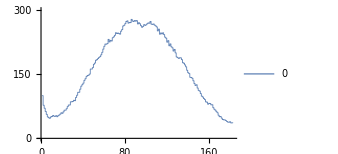
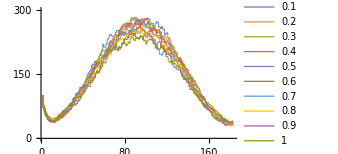
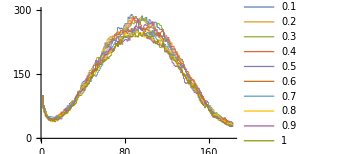
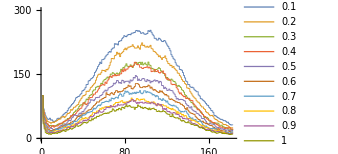
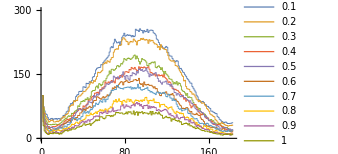
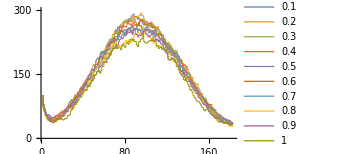
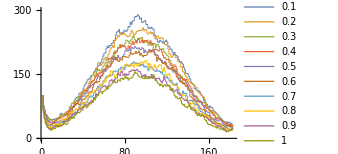
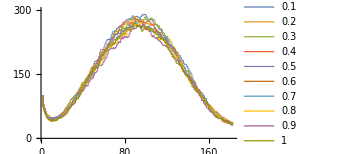
None | -Graphics-
ARE | -Graphics-
EAV | -Graphics- | IRS | -Graphics-
ITN | -Graphics-
IVM | -Graphics- | OVI | -Graphics-
ZOO | -Graphics-
None | -Graphics-

```mathematica
plots=Table[
temp=template[[j]];
(**)
stringPositions=StringPosition[names,temp];
indexes=Position[stringPositions,a_/;a≠{},1]//Flatten;
(**)
level=ToExpression[StringDelete[#,temp]&/@((StringSplit[#,"_"]&/@names[[indexes]])[[All,1]])];
levels=level//DeleteDuplicates;
trans={level,totalAdults[[indexes]]}//Transpose;
bins=Cases[trans,{#,__}]&/@levels;

plot=Table[
Mean/@(bins[[i]][[All,2]]//Transpose)//N
,{i,1,bins//Length}]//ListLinePlot[#,InterpolationOrder->0,ImageSize->250,PlotRange->{0,300},PlotLegends->Placed[levels,Below],PlotStyle->{{Thickness[.0025]}}]&
,{j,1,template//Length}];

{Grid[#,Background->{{LightBlue},None}]&/@Partition[{Style[#,25]&/@(Rotate[#,90Degree]&/@labels),plots}//Transpose,3,3,1]}//Grid[#]&
(*Export["linear.png",%,ImageSize->2000,ImageResolution->200]*)
```

## Radial Plots

### Animation

```mathematica
ratios=Table[
temp=template[[j]];
(**)
stringPositions=StringPosition[names,temp];
indexes=Position[stringPositions,a_/;a≠{},1]//Flatten;
(**)
level=ToExpression[StringDelete[#,temp]&/@((StringSplit[#,"_"]&/@names[[indexes]])[[All,1]])];
levels=level//DeleteDuplicates;
trans={level,totalAdults[[indexes]]}//Transpose;
bins=Cases[trans,{#,__}]&/@levels;

(Total/@Table[Mean/@(bins[[i]][[All,2]]//Transpose)//N,{i,1,bins//Length}])/Length[bins[[1,1,2]]]
,{j,1,template//Length}];
means=Flatten[{{Flatten[ConstantArray[ratios[[1]],10]]},ratios[[2;;All]]},1];
radialReady=means//Transpose;
```

```mathematica
stillFrames=PlotReview[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]],#[[1]]},""]&/@radialReady;
```

```mathematica
framesNumber=100;
(**)
max=radialReady//Length;
range=Range[0,max,max/framesNumber]//N;
functions=Interpolation[#]&/@(radialReady//Transpose);
(**)
points=Table[
Quiet[i[#]&/@range]
,{i,functions}]//Transpose;
frames=PlotReview[{#[[2,1]],#[[2,2]],#[[2,3]],#[[2,4]],#[[2,5]],#[[2,6]],#[[2,7]],#[[2,1]]},#[[1]]]&/@Transpose[{range*10,points}];
ListAnimate[frames]
(*Export["covgSweep.gif",frames,ImageResolution->80]*)
```

### Mean

```mathematica
frames=PlotReview2[{#[[2,1]],#[[2,2]],#[[2,3]],#[[2,4]],#[[2,5]],#[[2,6]],#[[2,7]],#[[2,8]]},#[[1]],#[[3]]]&/@Transpose[{ConstantArray["",radialReady//Length],radialReady,Hue[#]&/@Range[1/(Length[radialReady]),1,1/(Length[radialReady])]}];
Show[frames//Reverse,Frame->True,GridLines->{Range[-300,300,100],Range[-300,300,100]}]
(*Export["average.png",Rasterize[%,ImageResolution->200],ImageSize->2000]*)
```

## Animation

### Prepare Data

```mathematica
ratios=Table[
temp=template[[j]];
(**)
stringPositions=StringPosition[names,temp];
indexes=Position[stringPositions,a_/;a≠{},1]//Flatten;
(**)
level=ToExpression[StringDelete[#,temp]&/@((StringSplit[#,"_"]&/@names[[indexes]])[[All,1]])];
levels=level//DeleteDuplicates;
trans={level,totalAdults[[indexes]]}//Transpose;
bins=Cases[trans,{#,__}]&/@levels;
(**)
Table[Mean/@(bins[[i]][[All,2]]//Transpose)//N,{i,1,bins//Length}]
,{j,1,template//Length}];
means=Prepend[ratios[[2;;All]],Flatten[ConstantArray[ratios[[1]],10],1]];
```

### Single Coverage Level

```mathematica
coverageMeansNplets=(Transpose/@means);
labels;
sample=coverageMeansNplets[[All,90]][[All,3]]
(*Plot*)
RadialPlot[sample,labels,PlotStyle->{{Thick,Blue}}]
```

{274.5,270.8,271.,178.2,186.,271.6,229.6,272.7}

-Graphics-

### Mean Through Coverage Levels

```mathematica
meanNumberOfMosquitoes=Table[Mean/@i,{i,(Transpose/@coverageMeansNplets)}];
(*Plot*)
radialsMean=RadialPlot[#[[1]],labels,FontSize->25,PlotStyle->{{Thick,#[[2]]}},Axes->False,Frame->True]&/@Transpose[{
meanNumberOfMosquitoes//Transpose,
ColorData["TemperatureMap"][#]&/@Range[0,1+(1/Length[meanNumberOfMosquitoes]),(1/Length[meanNumberOfMosquitoes])]
}];
Show[radialsMean]
Export["average.png",%,ImageSize->1000]
```

### Animation

#### 2 D

```mathematica
numberOfMosquitoes=(coverageMeansNplets);

frames2=Table[
data=Transpose[numberOfMosquitoes[[All,j]]];
Show[Table[
RadialPlotRange[data[[i]],labels,{{-400,400},{-400,400}},385,ConstantArray[Range[-350,350,50],2],
GridLinesStyle->White,
PlotStyle->{{Thick,ColorData["TemperatureMap"][i/Length[data]]}},
Frame->True,
ImageSize->Large,
Axes->False
]
,{i,1,Length[data]}]]
,{j,1,Transpose[numberOfMosquitoes]//Length}];
```

```mathematica
(*Export["gifRadial.gif",frames2]*)
```

```mathematica
blackFrames=Show[#,Background->Black,GridLinesStyle->Opacity[.75],Axes->False,Frame->False]&/@frames2;
Export["gifRadial.gif",blackFrames,ImageSize->400,ImageResolution->150]
```

gifRadial.gif

#### 3 D (Should be improved)

```mathematica
ratios=Table[
temp=template[[j]];
(**)
stringPositions=StringPosition[names,temp];
indexes=Position[stringPositions,a_/;a≠{},1]//Flatten;
(**)
level=ToExpression[StringDelete[#,temp]&/@((StringSplit[#,"_"]&/@names[[indexes]])[[All,1]])];
levels=level//DeleteDuplicates;
trans={level,totalAdults[[indexes]]}//Transpose;
bins=Cases[trans,{#,__}]&/@levels;

Table[Mean/@(bins[[i]][[All,2]]//Transpose)//N,{i,1,bins//Length}]
,{j,1,template//Length}];
means=Prepend[ratios[[2;;All]],Flatten[ConstantArray[ratios[[1]],10],1]];
frames=Table[
coords=Table[means[[All,i]][[All,time]],{i,1,10}];
Table[
layers=CreateLayer[coords[[j]],j*30],{j,1,10}]
,{time,1,means[[1,1]]//Length}];
frames=Table[
Append[i,First[i]]
,{i,#}]&/@frames;
(**)
colors=Hue[#]&/@Range[.1,1,.1];
three=Table[
Graphics3D[
{
Specularity[Black,10],
Lighting->"Neutral",
Thickness[.0075],
Transpose[{colors,Line[#]&/@i}],
PointSize->.025,
Transpose[{colors,Sphere[#,6]&/@i}](*,
Opacity[0],
Cylinder[{{0,0,0},{0,0,300}},300],
Cylinder[{{0,0,0},{0,0,300}},200],
Cylinder[{{0,0,0},{0,0,300}},100]*)
}
,PlotRange->{{-300,300},{-300,300},{0,300}},AspectRatio->1,AxesEdge->{{-1,-1},{1,-1},None},Axes->True,ImageSize->500,Boxed->True,FaceGrids->{{0,0,-1}},BoxStyle->Directive[Dashed]]
,{i,frames}];
three[[1]]
```

#### Both

```mathematica
pairs=Transpose[{frames2,three}];
grid=Grid[{#}]&/@pairs;
```

```mathematica
grid[[10]]
(*Export["gifRadial3D.gif",grid]*)
```

## Legacy

```mathematica
Options[RadialPlotRange]={Frame->False,FontSize->15,ImageSize->Medium,FontAngle->45Degree,PlotMarkers->{Automatic,Tiny},Joined->True,PlotStyle->{{Thickness[.005]}},AxesStyle->Directive[Gray,10],Axes->True,GridLinesStyle->Directive[Thickness[.0025],Dashed,Gray],PlotRange->Automatic,PolarGridLines->Automatic};
RadialPlotRange[values_,labels_,range_,labelDistance_,gridLines_,OptionsPattern[]]:=Module[{degreeIncrement,degrees,transposed,max,labelsPairs,sample=values},
degreeIncrement=(360/(sample//Length))Degree;
degrees=Range[0,(360-1)Degree,degreeIncrement];
transposed=Transpose[{degrees,sample}];
labelsPairs=Transpose[{labels,PolarToRectangularCoordinates[#,labelDistance]&/@degrees}];
max=Max[transposed[[All,2]]];
list=ListPolarPlot[
Append[transposed,First[transposed]]
,Frame->OptionValue[Frame]
,Epilog->{Rotate[Style[Text[#[[1]],#[[2]]],Bold,OptionValue[FontSize]],OptionValue[FontAngle]]&/@labelsPairs}
,PlotMarkers->OptionValue[PlotMarkers]
,Joined->OptionValue[Joined]
,PlotStyle->OptionValue[PlotStyle]
,InterpolationOrder->1
,AxesStyle->OptionValue[AxesStyle]
,Axes->OptionValue[Axes]
,ImageSize->OptionValue[ImageSize]
,GridLines->gridLines
,GridLinesStyle->OptionValue[GridLinesStyle]
,PlotRange->range
,PolarGridLines->False
];
graph=Graphics[{
Gray,
Thin,
Circle[{0,0},#]&/@Range[0,Max[gridLines[[1]]],50],
Line[{{0,0},#}]&/@(PolarToRectangularCoordinates[#,Max[gridLines[[1]]]]&/@degrees)
}];
Show[{list,graph}]
]
```

```mathematica
Graphics[
{
Gray,Circle[{0,0},#]&/@Range[0,300,50],
Line[{{0,0},#}]&/@linesCoords,
Thickness[.0025],
Transpose[{colors,Line[#]&/@i}],
PointSize[Large],
Transpose[{colors,Point[#]&/@i}],
Style[Text[#[[1]],#[[2]]+10],Bold,15]&/@Transpose[{RotateRight[labels,1],textCoords[[1;;Length[textCoords]-1]]}]
}
,PlotRange->{{-375,375},{-375,375}},AspectRatio->1,ImageSize->500]
```

### Animation (Should Only Be )

```mathematica
ratios=Table[
temp=template[[j]];
(**)
stringPositions=StringPosition[names,temp];
indexes=Position[stringPositions,a_/;a≠{},1]//Flatten;
(**)
level=ToExpression[StringDelete[#,temp]&/@((StringSplit[#,"_"]&/@names[[indexes]])[[All,1]])];
levels=level//DeleteDuplicates;
trans={level,totalAdults[[indexes]]}//Transpose;
bins=Cases[trans,{#,__}]&/@levels;

Table[Mean/@(bins[[i]][[All,2]]//Transpose)//N,{i,1,bins//Length}]
,{j,1,template//Length}];
means=Prepend[ratios[[2;;All]],Flatten[ConstantArray[ratios[[1]],10],1]];
(**)
frames=Table[
coords=Table[
means[[All,i]][[All,time]]
,{i,1,10}];
Table[CreateLayer[coords[[j]],j],{j,1,10}]//ListPointPlot3D[#,Filling->Bottom,PlotRange->{{-300,300},{-300,300},{0,10}},PlotStyle->Directive[Opacity[0],Purple, Specularity[White,50]]]&
,{time,1,150}];
(**)
ListAnimate[frames];
```

```mathematica
frames=Table[
coords=Table[means[[All,i]][[All,time]],{i,1,10}];
Table[
layers=CreateLayer[coords[[j]],j*30],{j,1,10}]
,{time,1,means[[1,1]]//Length}];
frames=Table[
Append[i,First[i]]
,{i,#}]&/@frames;
(**)
colors=Hue[#]&/@Range[.1,1,.1];
three=Table[
Graphics3D[
{
Thick,
Transpose[{colors,Line[#]&/@i}],
Transpose[{colors,Point[#]&/@i}],
Opacity[0],
Cylinder[{{0,0,0},{0,0,300}},300],
Cylinder[{{0,0,0},{0,0,300}},200],
Cylinder[{{0,0,0},{0,0,300}},100]
}
,PlotRange->{{-300,300},{-300,300},{0,300}},AspectRatio->1,ImageSize->500]
,{i,frames}];
ListAnimate[%];
(**)
(*ListAnimate[frames]*)
```

```mathematica
labels={"ARE","None","EAV","IRS","ITN","IVM","OVI","ZOO"};
frames=Table[
coords=Table[means[[All,i]][[All,time]],{i,1,10}];
Table[
layers=CreateLayer[coords[[j]],j*30],{j,1,10}]
,{time,1,means[[1,1]]//Length}];
frames=Table[
Append[i,First[i]][[All,1;;2]]
,{i,#}]&/@frames;
two=Table[
angles=(ArcTan[#[[2]],#[[1]]]&/@#&/@frames[[1]])[[1]];
textCoords=PolarToRectangular2[#,350]&/@angles;
linesCoords=PolarToRectangular3[#,300]&/@angles;
Graphics[
{
Gray,Circle[{0,0},#]&/@Range[0,300,50],
Line[{{0,0},#}]&/@linesCoords,
Thickness[.0025],
Transpose[{colors,Line[#]&/@i}],
PointSize[Large],
Transpose[{colors,Point[#]&/@i}],
Style[Text[#[[1]],#[[2]]+10],Bold,15]&/@Transpose[{RotateRight[labels,1],textCoords[[1;;Length[textCoords]-1]]}]
}
,PlotRange->{{-375,375},{-375,375}},AspectRatio->1,ImageSize->500]
,{i,frames}];
(*Export["test.gif",%,ImageResolution->100]*)
```

```mathematica
Grid[{{Style["Day: "<>ToString[#[[3]]],30]},{Grid[{{#[[1]],#[[2]]}}]}}]&/@Transpose[{two,three,Range[1,2*Length[three],2]}];
ListAnimate[%];
(*Export["test2.gif",%%,ImageResolution->100]*)
```

```mathematica
coverageMeansNplets=(Transpose/@means);
labels
sample=coverageMeansNplets[[All,90]][[All,5]]



RadialPlot[sample]
```

```mathematica
degreeIncrement=(360/(sample//Length))Degree;
degrees=Range[0,(360-1)Degree,degreeIncrement];
transposed=Transpose[{degrees,sample}]
labelsPairs=Transpose[{labels,PolarToRectangularCoordinates[#,(max+max*.25)]&/@degrees}];
max=Max[transposed[[All,2]]];
ListPolarPlot[
Append[transposed,First[transposed]]
,Frame->False
,Epilog->{Rotate[Style[Text[#[[1]],#[[2]]],Bold,15],45Degree]&/@labelsPairs}
,PlotMarkers->{Automatic,Medium}
,Joined->True
,PlotStyle->{{Thickness[.005]}}
,InterpolationOrder->1
,AxesStyle->Directive[Gray,10]
,Axes->True
(*,GridLines->ConstantArray[Range[-max*2,max*2,100],2]*)
,GridLinesStyle->Directive[Thickness[.0025],Dashed,Gray]
,PlotRange->{{-(max+max*.5),max+max*.5},{-(max+max*.5),max+max*.5}}
,PolarGridLines->{Table[i*Degree,{i,0,360,45}],Range[0,10000,50]}
]
```